# GrayCode

GrayCode[n]
gives the Gray code of the integer n.

## See AlsoSeeAlsoInsert links to any related reference (function) pages.

"XXXX" ▪

## Tech NotesTechNotesInsert links to related tech notes.

## Related Guides

## Related LinksRelatedLinksInsert links to any related page, including web pages.

## Examples InitializationExamplesInitializationInput that is to be evaluated before any examples are run, e.g. Needs[…].

```mathematica
Needs["PeterBurbery`CombinatoricsPaclet`"]
```

## Basic Examples | More Examples ⊳

Find the Gray code of an integer:

```mathematica
GrayCode[14]
```

{1,0,0,1}

GrayCode threads itself elementwise over lists:

```mathematica
GrayCode[Range[25]]
```

{{1},{1,1},{1,0},{1,1,0},{1,1,1},{1,0,1},{1,0,0},{1,1,0,0},{1,1,0,1},{1,1,1,1},{1,1,1,0},{1,0,1,0},{1,0,1,1},{1,0,0,1},{1,0,0,0},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,1},{1,1,0,1,0},{1,1,1,1,0},{1,1,1,1,1},{1,1,1,0,1},{1,1,1,0,0},{1,0,1,0,0},{1,0,1,0,1}}

## More ExamplesMoreExamplesExtended examples in standardized sections.

### Scope

### Generalizations & Extensions

### Options

### Applications

Visualize the sequence of values generated by GrayCode:

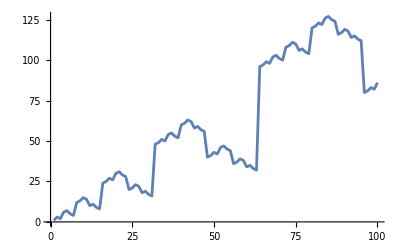

```mathematica
ListLinePlot[Table[FromDigits[GrayCode[n],2],{n,100}]]
```

### Properties & Relations

Successive values differ in only one bit in the binary representation:

```mathematica
gc=PadLeft[GrayCode[Range[15]],{15,4}]
```

{{0,0,0,1},{0,0,1,1},{0,0,1,0},{0,1,1,0},{0,1,1,1},{0,1,0,1},{0,1,0,0},{1,1,0,0},{1,1,0,1},{1,1,1,1},{1,1,1,0},{1,0,1,0},{1,0,1,1},{1,0,0,1},{1,0,0,0}}

```mathematica
diff=Differences[gc]
```

{{0,0,1,0},{0,0,0,-1},{0,1,0,0},{0,0,0,1},{0,0,-1,0},{0,0,0,-1},{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,0,0,-1},{0,-1,0,0},{0,0,0,1},{0,0,-1,0},{0,0,0,-1}}

Visualize the differences:

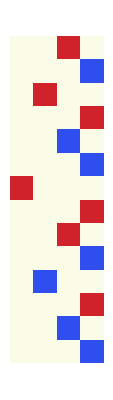

```mathematica
ArrayPlot[diff,ColorFunction->"TemperatureMap"]
```

### Possible Issues

### Interactive Examples

### Neat Examples

Create an animated fractal from the sequence generated by GrayCode:

```mathematica
ResourceFunction["SimpleListAnimate"][Table[ListLinePlot[Table[FromDigits[GrayCode[n],2],{n,2^m-1}],Axes->False],{m,10}]]
```

## Metadata

### CategorizationMetadataMetadata such as page URI, context, and type of documentation page.

Symbol

PeterBurbery/CombinatoricsPaclet

PeterBurbery`CombinatoricsPaclet`

PeterBurbery/CombinatoricsPaclet/ref/GrayCode

### Keywords

### Syntax Templates